## Singular Perturbation

```mathematica
eq:={y''[t]+0.01y'[t]+y[t]==0,y[0]==1,y'[0]==0}
```

```mathematica
NDSolve[eq,y[t],{t,0,1}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
{yans[t_]}={y[t]}/.Flatten[NDSolve[eq,y[t],{t,0,1}]]
```

{InterpolatingFunction[…][t]}

```mathematica
graphy=Plot[yans[t],{t,0,1},AxesLabel->{"x","y"},PlotLabel->"Numerical Solution of y"];
```

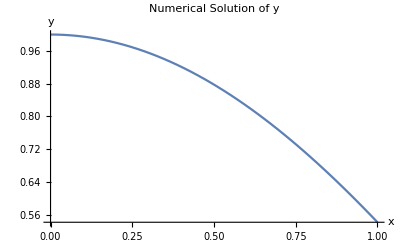

```mathematica
Show[graphy]
```

```mathematica
yhand[x_]:=ⅇ^((-0.01 x)/2) Cos[x]
```

```mathematica
graphyh=Plot[yhand[x],{x,0,1},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y"];
```

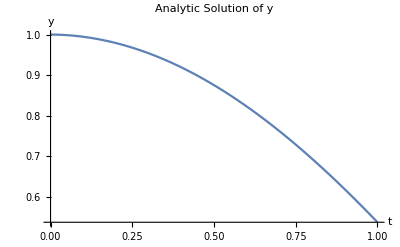

```mathematica
Show[graphyh]
```

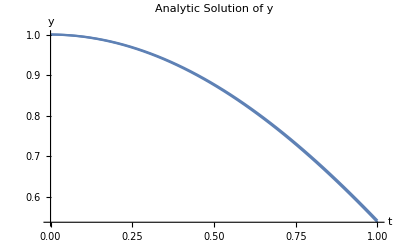

```mathematica
Show[graphyh,graphy]
```